```mathematica
sol=NDSolve[{x''[t]==-0.023*x'[t]*Sqrt[x'[t]^2+y'[t]^2],y''[t]==-9.81-0.023*y'[t]*Sqrt[x'[t]^2+y'[t]^2],x[0]==0,x'[0]==10.61,y[0]==2,y'[0]==10.61},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

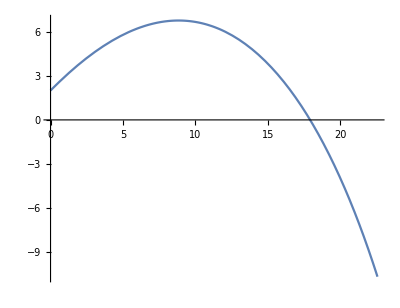

```mathematica
ParametricPlot[{x[t]/.sol[[1]],y[t]/.sol[[1]]},{t,0,3}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

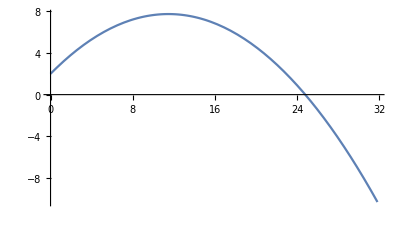

```mathematica
sol=NDSolve[{x''[t]==0,y''[t]==-9.81,x[0]==0,x'[0]==10.61,y[0]==2,y'[0]==10.61},{x,y},{t,0,100}]
ParametricPlot[{x[t]/.sol[[1]],y[t]/.sol[[1]]},{t,0,3}]
```

{{y'→InterpolatingFunction[…]}}

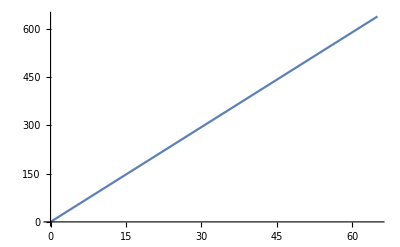

```mathematica
sol=NDSolve[{y''[t]==9.81,y[0]==-20000,y'[0]==0},y',{t,0,65}]
Plot[y'[t]/.sol[[1]],{t,0,65}]
```

{{y→InterpolatingFunction[…]}}

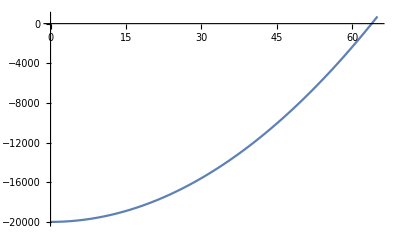

```mathematica
sol=NDSolve[{y''[t]==9.81,y[0]==-20000,y'[0]==0},y,{t,0,65}]
Plot[y[t]/.sol[[1]],{t,0,65}]
```

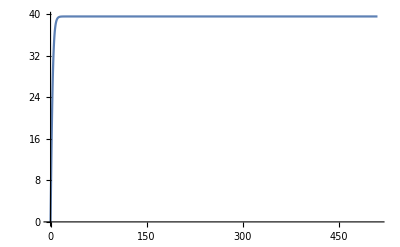

```mathematica
y'[t_]:=39.6*Tanh[9.8*t/39.6]
Plot[y'[t],{t,0,510}]
```

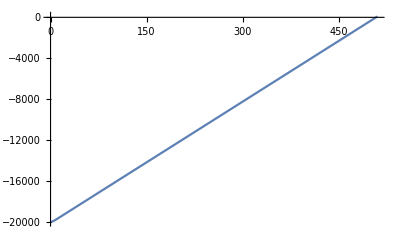

```mathematica
y[t_]:=39.6^2/9.8*Log[Cosh[9.8*t/39.6]]-20000
Plot[y[t],{t,0,510}]
```

```mathematica
sol=NDSolve[{y''[t]==9.81-((0.5*(Exp[(y[t]/8000)]))/80)*(y'[t])^2,y[0]==-8000,y'[0]==0},y'[t],{t,0,170}]
Plot[y'[t] /. sol,{t,0,170}]
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {9.8 Sech[0.247475 t]^2==9.81-9.801 ⅇ^((-20000+Times[«2»])/8000) Tanh[0.247475 t]^2,False,True}.

NDSolve[{9.8 Sech[0.247475 t]^2==9.81-9.801 ⅇ^((-20000+160.016 Log[Cosh[0.247475 t]])/8000) Tanh[0.247475 t]^2,False,True},39.6 Tanh[0.247475 t],{t,0,170}]

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},0.034034,{0.00347286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},0.034034,{0.00347286,0.,170.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 3.47286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{False,False,True},27.5605,{3.47286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
sol=NDSolve[{y''[t]==9.81-((0.5*(Exp[(y[t]/8000)]))/80)*(y'[t])^2,y[0]==-8000,y'[0]==0},y[t],{t,0,170}]
Plot[y[t] /. sol,{t,0,170}]
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {9.8 Sech[0.247475 t]^2==9.81-9.801 ⅇ^((-20000+Times[«2»])/8000) Tanh[0.247475 t]^2,False,True}.

NDSolve[{9.8 Sech[0.247475 t]^2==9.81-9.801 ⅇ^((-20000+160.016 Log[Cosh[0.247475 t]])/8000) Tanh[0.247475 t]^2,False,True},-20000+160.016 Log[Cosh[0.247475 t]],{t,0,170}]

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},-20000.,{0.00347286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},-20000.,{0.00347286,0.,170.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 3.47286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{False,False,True},-19947.,{3.47286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
sol=NDSolve[{y''[t]==(6.673*10^(-11)*5.98*10^(24)/((-6371000-y[t])^2))+-((0.5*(Exp[(y[t]/8000)]))/80)*(y'[t])^2,y[0]==-8000,y'[0]==0},y'[t],{t,0,170}]
Plot[y'[t] /. sol,{t,0,170}]
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {9.8 Sech[0.247475 t]^2==(3.99045×10^14)/(-6351000-160.016 Log[«1»])^2-9.801 ⅇ^((-20000+Times[«2»])/8000) Tanh[0.247475 t]^2,False,True}.

NDSolve[{9.8 Sech[0.247475 t]^2==(3.99045×10^14)/(-6351000-160.016 Log[Cosh[0.247475 t]])^2-9.801 ⅇ^((-20000+160.016 Log[Cosh[0.247475 t]])/8000) Tanh[0.247475 t]^2,False,True},39.6 Tanh[0.247475 t],{t,0,170}]

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},0.034034,{0.00347286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},0.034034,{0.00347286,0.,170.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 3.47286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{False,False,True},27.5605,{3.47286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
sol=NDSolve[{y''[t]==(6.673*10^(-11)*5.98*10^(24)/((-6371000-y[t])^2))+-((0.5*(Exp[(y[t]/8000)]))/80)*(y'[t])^2,y[0]==-8000,y'[0]==0},y[t],{t,0,170}]
Plot[y[t] /. sol,{t,0,170}]
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {9.8 Sech[0.247475 t]^2==(3.99045×10^14)/(-6351000-160.016 Log[«1»])^2-9.801 ⅇ^((-20000+Times[«2»])/8000) Tanh[0.247475 t]^2,False,True}.

NDSolve[{9.8 Sech[0.247475 t]^2==(3.99045×10^14)/(-6351000-160.016 Log[Cosh[0.247475 t]])^2-9.801 ⅇ^((-20000+160.016 Log[Cosh[0.247475 t]])/8000) Tanh[0.247475 t]^2,False,True},-20000+160.016 Log[Cosh[0.247475 t]],{t,0,170}]

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},-20000.,{0.00347286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},-20000.,{0.00347286,0.,170.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 3.47286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{False,False,True},-19947.,{3.47286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
sol=NDSolve[{y''[t]==9.81-(0.5/80)*y'[t]^2*Exp[y[t]/8000],y[0]==-8000,y'[0]==0},y''[t],{t,0,170}]
Plot[y''[t]/.sol,{t,0,170}]
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {9.8 Sech[0.247475 t]^2==9.81-9.801 ⅇ^((-20000+Times[«2»])/8000) Tanh[0.247475 t]^2,False,True}.

NDSolve[{9.8 Sech[0.247475 t]^2==9.81-9.801 ⅇ^((-20000+160.016 Log[Cosh[0.247475 t]])/8000) Tanh[0.247475 t]^2,False,True},9.8 Sech[0.247475 t]^2,{t,0,170}]

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},9.79999,{0.00347286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{False,False,True},9.79999,{0.00347286,0.,170.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 3.47286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{False,False,True},5.05311,{3.47286,0,170}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-